```mathematica
{m,n}={5,5};
A=RandomReal[{-1,1},{m,n}];
MatrixPlot[A,PlotLegends->Automatic];
b=SparseArray[1->1,m];
LinearSolve[A,b];

Eigenvalues[A]
SingularValueList[A]
```

{1.33237+0. ⅈ,-1.05406+0.725327 ⅈ,-1.05406-0.725327 ⅈ,-0.00292915+0.358002 ⅈ,-0.00292915-0.358002 ⅈ}

{2.01255,1.62731,1.19962,0.646985,0.109991}

```mathematica
{m,n}={5,6};
B=RandomReal[{-1,1},{m,n}];
A=B.Transpose[B];
MatrixPlot[A];
Eigenvalues[A]
```

{4.56963,2.62048,1.94614,0.208922,0.132316}

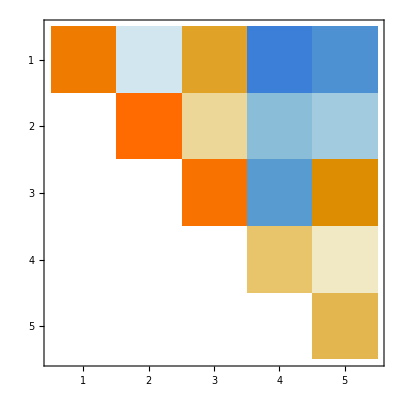

3.68219×10^-16

```mathematica
U=CholeskyDecomposition[A];
MatrixPlot[U]
Norm[A-Uᵀ.U,"Frobenius"]
```